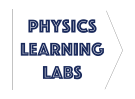
# -Graphics- Lab 7 - Torque

## Background

The rotational apparatus is the same as in Lab 6; a hanging mass supplies a tension force upon the pulley, providing a torque which induces an angular acceleration of all objects attached to the rotational platform. In this lab, the rotating objects will always consist of a single square mass and the platform itself.

```mathematica
-Graphics--Graphics-
```

According to Prelab 7, we have found that if the hanging mass’s acceleration is slow in comparison to gravity, then the tension is approximately T=m_h g, whereby the magnitude of the torque acting on the rotational system can be expressed as

τ = m_h g r.

Using τ= Iα, we may then express the angular acceleration of the rotational apparatus as

α=(m_h g r)/I

with hanging mass m_h, pulley radius r, and total inertia I (platform + square mass). The pulley has three possible radii, denoted r_1, r_2, and r_3:

The total inertia can be expressed as a linear superposition of the platform and square mass (see Fig.(1)),

I=I_p+I_s.

According to Eq.(2), the angular acceleration α can be changed by modifying either the hanging mass weight, the radius of the pulley, or the system’s inertia. We will explore the effect of hanging mass and radius in Part A, and inertia in Part B.

## Procedure

### General Procedure Steps

Power on the Pasco 850 Universal Interface and open Lab_7.cap

For each trial, wind up the pulley by rotating the platform. Wind the pulley until top surface of hanging mass is level with bottom surface of table. Keep a hand on the platform of interest to prevent the hanging mass from falling.

Stop recording before the hanging mass has reached the bottom of its travel.

Protip: Let the angular momentum of the object re-wind the pulley for you during the upward ascent.

When changing the pulley or square mass position, relieve the tension on the pulley by placing the hanging mass on the table

Before starting a new trial, you must label the data run according to the Data Labeling instructions below.

Use  to display plots of single or multiple trials

Select the desired data on the graph and use the  tool to determine the slope for the entire range of data. To select a different run, click on a different set of data or click the corresponding label in the legend.

### Data Labeling

Navigate to the Data Summary tab

Under Angle (rad), label the most recent run according to the respective configuration as indicated in the Experiment section

### Moving the Square Mass

To move the square mass, slightly loosen the wing-nut  and slide the square nut to desired position. Tighten the wing-nut  until the square is secure (do NOT over-torque the wing-nut). Center the square mass at the respective position - Fig.(5) an example for Platform-Square-5cm.

### Measuring the Pulley Radii

Use the provided digital caliper to find the diameter (in SI units) of each pulley. Record this data for use in the analysis section.

### Switching the Pulley

Pulley 1 (r_1): The string must be threaded through the groove of Pulley 2 before winding Pulley 1, as seen below.

```mathematica
-Graphics--Graphics-
```

Pulley 2 (r_2): No special instructions needed

Pulley 3 (r_3): The string must be threaded through the groove of Pulley 3 before winding Pulley 3, as seen below. To avoid complications with the knot, try to wind Pulley 3 on the lower portion of the pulley. This can be achieved by lightly holding a finger downward while winding.

```mathematica
-Graphics- -Graphics- -Graphics-
```

## Experiment

In Part A, we will first measure the angular acceleration corresponding to a particular configuration of hanging masses. Then we will vary the pulley radius and hanging masses to determine the correct configuration that yields approximately the same angular acceleration.

In Part B, we will first measure the angular acceleration corresponding to a particular configuration of hanging masses. Then we will adjust the hanging mass and vary the position of the square mass on the platform to determine the correct configuration that yields approximately the same angular acceleration.

### Part A: Varying m_h and r

Navigate to the Part A page in Capstone

Wind the pulley of radius r_2 with a total hanging mass of 60g (recall the weight of the hanger is 20g). Release the hanging mass and record the angular velocity ω. Label this trial as r2-60g. By taking the slope dω/dt, find the angular acceleration of this configuration. We will refer to this angular acceleration as α_A. Store the value of the angular acceleration as variable αA below.

```mathematica
αA= ;
```

Using pulley radius r_1, use trial and error in order to find the hanging mass required such that the angular acceleration is approximately the same as α_A. The hanging mass may be changed in increments of 10g. Record and label each trial within Capstone as r1-XXg, where XX denotes the total hanging mass. (The result of this configuration will be used to answer questions in the analysis section).

Using pulley radius r_3, use trial and error in order to find the hanging mass required such that the angular acceleration is the same as α_A. The hanging mass may be changed in increments of 10g. Record and label each trial within Capstone as r3-XXg, where XX denotes the total hanging mass. (The result of this configuration will be used to answer questions in the analysis section).

Hint: You can try coming up with a calculated estimate of the correct hanging mass to reduce the number of required trials.

### Part B: Varying I

Navigate to the Part B page in Capstone

Wind pulley radius r_2 with a total hanging mass of 80g (recall the weight of the hanger is 20g). Release the hanging mass and record the angular velocity ω. Label this trial as r2-80g-0cm. By taking the slope dω/dt, find the angular acceleration of this configuration. We will refer to this angular acceleration as α_B. Store the value of the angular acceleration as variable αB below.

```mathematica
αB= ;
```

Continuing using pulley radius r_2 and attach a total hanging mass of 100g. Now vary the position of the square mass along the platform in increments of 5 cm in order to find the correct position that yields the same approximate angular acceleration as α_B. Possible positions are {0, 5, 10, 15, 20, 25} cm. Record and label each trial within Capstone as r2-100g-XXcm, where XX denotes the position of the square mass.

Record the position of the square mass that resulted in an angular acceleration that was closest to α_B. We will use this radius to answer questions in the analysis section. Store this radius as variable rs below

```mathematica
rs= ;
```

Hint: You can try coming up with a calculated estimate of the correct inertia to reduce the number of required trials.

#### Example

To ensure that you have found the right configuration, some of your trials must at least probe above and below the desired acceleration. In the example of Fig.(11), the red line represents ω_A, the green line represents the correct mass configuration, and the blue and purple lines probe above and below ω_A.

## Analysis

### Reference Equations

τ = m_h g r

α=(m_h g r)/I

I=I_p+I_s

### Part A

Paste an image of the Capstone plot representing α_A and all trials for pulley radius r_1. (See procedure for how to show selected trials only).

Paste an image of the Capstone plot representing α_A and all trials for pulley radius r_3.

Based on your experiment using pulley radius r_1, what hanging mass provided an angular acceleration closest to α_A? We will denote this as m_h_exp.

Based on your experiment using pulley radius r_3, what hanging mass provided an angular acceleration closest to α_A?

Use Eq.(1) along with the values of r_2 and m_h to calculate the torque τ_A corresponding to reference configuration α_A.

Use the measured value of r_1 (m) and the torque τ_A (from Q5) to estimate the hanging mass required to match the angular acceleration α_A. (Refer to Eq.(1) if needed). We will denote this as m_h_calc.

How does the hanging mass m_h_expr compare to m_h_calc? Relate this to the difference in ω(t) as given in your plot.

Imagine there were a fourth pulley of radius r_4= 5 mm. What hanging mass would be required to match the angular acceleration of α_A?

### Part B

Paste an image of the Capstone plot representing α_B and all trials for the various positions of the square mass.

Use Eq.(2) along with the values of m_h, r_2, and α_B, to calculate the inertia corresponding to the reference configuration α_B. We will denote this inertia as I_p (platform inertia).

You have determined the value of r_s (i.e. the variable rs) that yields an angular acceleration closest to α_B. For this trial, use Eq.(2) along with the measured values of m_h, r_2, and α to determine the inertia. We will denote this inertia as I (the experimental inertia of the platform and square mass).

How does I_p compare to I ? As the hanging mass increases, does the required inertia increase or decrease in order to yield the same angular acceleration as α_B?

Weigh the mass of the square, denoting as m_s. Using m_s and r_s, calculate the moment of inertia I_s of the square mass at position r_s, approximating it as a point particle.

Using your previous results (Q10 and Q13), calculate the total estimated inertia I_p+I_s. How does this compare to the experimental inertia I?  Can you account for any presumable discrepancies between the calculated inertia and the experimental?

Use a few sentences to provide a detailed summary of this lab. 
Things to consider: What were the objectives and how did our experiment meet these objectives? What did you learn about torque? What is the dependence of torque upon pulley radius and hanging mass? How does the angular acceleration depend on inertia? What happened as you moved the square mass away from the center? (Refer to specific examples/plots and use quantitative data if possible).

# Submit this completed notebook as a .pdf into HuskyCT. (Make sure all cells sections are visible to receive credit for all your output. As a shortcut, use CTRL+A then CTRL+SHIFT+[ to open all cell sections).